```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
startpoints = Import["../data/problem1.txt","table"];
startpoints2 = Import["../data/problem2.txt","table"];
mainpoints = Delete[startpoints,1]
```

{{1.11152,0.475459},{-1.00095,0.151549},{-0.0380269,-0.485426},{-1.54083,0.946829},{-0.145701,-0.508304},{-0.721142,0.262097},{-1.07488,0.64107},{0.187675,0.124366},{-0.32008,-0.58109},{-1.29675,0.845146},{-1.17331,0.580694},{-0.852551,0.737298},{0.665409,0.452545},{-1.63423,-0.617773},{1.17274,0.12744},{0.815421,-0.468176},{-0.58242,0.409693},{1.49489,0.377652},{0.483578,0.679537},{1.28229,0.708425}}

```mathematica
$HistoryLength = 0;
```

```mathematica
QuickSelect[ls_List,index_Integer,lo_:1,hi_:None,depth_:0]:=Block[{pivot,cur,newLs=ls,hiVal=If[hi===None,Length[ls],hi]},If[lo==hiVal,Return[newLs[[lo]]]];pivot=RandomInteger[{lo,hiVal}];
newLs=ReplacePart[newLs,{lo->newLs[[pivot]],pivot->newLs[[lo]]}];
cur=lo;
Do[If[newLs[[i]]<newLs[[lo]],cur++;
newLs=ReplacePart[newLs,{cur->newLs[[i]],i->newLs[[cur]]}]],{i,lo+1,hiVal}];
newLs=ReplacePart[newLs,{cur->newLs[[lo]],lo->newLs[[cur]]}];
Which[index<cur,QuickSelect[newLs,index,lo,cur-1,depth+1],index>cur,QuickSelect[newLs,index,cur+1,hiVal,depth+1],True,newLs[[cur]]]]
```

```mathematica
Bridge[points_,verticalline_]:=Block[{left,right,medianslope, maxslope,maxset,maxtableofb,pairs,large,equal,small,candidates,xpair,slopes,filteredPoints,medindex},
candidates={};
pairs={};
If[Length[points]==2,Return[Sort[points]]];
If[OddQ[Length[points]],candidates=Join[candidates,{points[[-1]]}]];
pairs=Map[SortBy[#,First]&,Partition[points,2,2]];
filteredPoints=ParallelMap[If[#[[1,2]]>#[[2,2]],#[[1]],#[[2]]]&,Cases[pairs,{{x_,y_},{u_,v_}}/;x==u]];
candidates=Join[candidates,filteredPoints];
pairs=DeleteCases[pairs,{{x_,y_},{u_,v_}}/;x==u];
slopes=Table[(pairs[[i,2,2]]-pairs[[i,1,2]])/(pairs[[i,2,1]]-pairs[[i,1,1]]),{i,1,Length[pairs]}];
If[EvenQ[Length[slopes]]==True,medindex=Quotient[Length[slopes],2],medindex=Quotient[Length[slopes],2]+1];
medianslope=QuickSelect[slopes,medindex];

small=Cases[pairs,{{a_,b_},{c_,d_}}/;((d-b)/(c-a))<medianslope-10^-9];
equal=Cases[pairs,{{a_,b_},{c_,d_}}/;Abs[((d-b)/(c-a))-medianslope]<10^-9];
large=Cases[pairs,{{a_,b_},{c_,d_}}/;((d-b)/(c-a))>medianslope+10^-9];
maxtableofb=Table[{points[[i,2]]-medianslope*points[[i,1]],points[[i]]},{i,1,Length[points]}];
maxslope=Sort[maxtableofb,#1[[1]]>#2[[1]] &][[1,1]];
maxset=Cases[points,{x_,y_}/;Abs[y-medianslope*x-maxslope]<10^-9:>{x,y}];
left=Cases[maxset,{x_,y_}/;x==Min[maxset[[All,1]]]:>{x,y}][[1]];
right=Cases[maxset,{x_,y_}/;x==Max[maxset[[All,1]]]:>{x,y}][[1]];
If[left[[1]]<=verticalline&&right[[1]]>verticalline,Return[{left,right}]];
If[right[[1]]<=verticalline,candidates=Join[candidates,Cases[Union[equal,large],{{a_,b_},{c_,d_}}:>{c,d}]];
candidates=Join[candidates,Flatten[small,1]]];
If[left[[1]]>verticalline,candidates=Join[candidates,Cases[Union[equal,small],{{a_,b_},{c_,d_}}:>{a,b}]];
candidates=Join[candidates,Flatten[large,1]]];
(*Print["current cands:",candidates];*)
Return[Bridge[candidates,verticalline]];

]
```

```mathematica
ConnectPoints[lower_,upper_,points_]:=Block[{pointsleft,pointsright,left,right,maxleft,minright},
If[lower==upper,Return[{lower}]];
maxleft = QuickSelect[points,Quotient[Length[points],2]+1];
minright = QuickSelect[points,Quotient[Length[points],2]];
{left,right} = Bridge[points,(maxleft[[1]]+minright[[1]])/2];
pointsleft = {left}~Join~Cases[points,{a_,b_}/;a<left[[1]]:>{a,b}];
pointsright = {right}~Join~Cases[points,{a_,b_}/;a>right[[1]]:>{a,b}];
Return[Join[ConnectPoints[lower,left,pointsleft],ConnectPoints[right,upper,pointsright]]];

]
```

```mathematica
UpperHull[points_]:=Block[{lower,upper,T},
T={};
lower=SelectFirst[points,#[[1]]==Min[points[[All,1]]]&&#[[2]]==Max[Cases[points,{x_,y_}/;x==Min[points[[All,1]]]:>{x,y}][[All,2]]]&];
upper=SelectFirst[points,#[[1]]==Max[points[[All,1]]]&&#[[2]]==Max[Cases[points,{x_,y_}/;x==Max[points[[All,1]]]:>{x,y}][[All,2]]]&];
If[upper==lower,Return[{lower}]];
T = DeleteDuplicates[Join[T,{lower},{upper},Cases[points,{x_,y_}/;lower[[1]]<x<upper[[1]]:>{x,y}]]];
Return[ConnectPoints[lower,upper,T]];
];
```

```mathematica
LowerHull[points_]:=Block[{invertedPoints,invertedHull},invertedPoints=points/. {x_,y_}:>{-x,-y};
invertedHull=UpperHull[invertedPoints];
invertedHull/. {x_,y_}:>{-x,-y}];
```

```mathematica
Convexhull [points_]:=Block[{upperhull,lowerhull},
upperhull = UpperHull[points];

lowerhull = LowerHull[points];

If[Last[upperhull]===First[lowerhull],upperhull=Most[upperhull]];
(*If[First[upperhull]===Last[lowerhull],lowerhull=Most[lowerhull]];*);
Return[Join[upperhull,lowerhull]];
]
```

```mathematica
$RecursionLimit = 3000;
```

```mathematica
Main []:=Block[{mainpoints,n,ch,t},
startpoints = Import["../data/problem1.txt","table"];
mainpoints = DeleteDuplicates@Delete[startpoints,1];

t=AbsoluteTiming[ch = Convexhull[mainpoints]][[1]];
Print["Количество точек выпуклой оболочки: ", Length[ch]-1];
Print["Время: ",t];
Print[ "Точки: ", ch];
gr =Show[ListPlot[ch,Joined->True,PlotStyle->Darker@Green],ListPlot[mainpoints],PlotRange->{-1,1}]
]
```

Количество точек выпуклой оболочки: 6

Время: 0.0175968

Точки: {{-1.63423,-0.617773},{-1.54083,0.946829},{1.28229,0.708425},{1.49489,0.377652},{0.815421,-0.468176},{-0.32008,-0.58109},{-1.63423,-0.617773}}

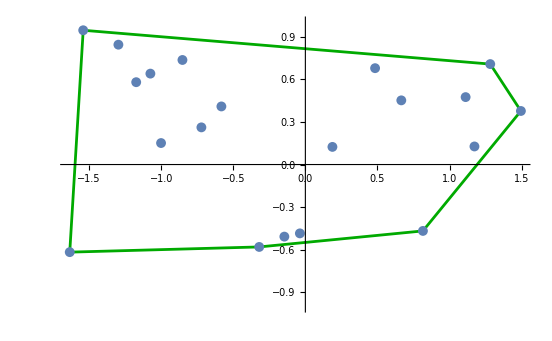

```mathematica
ClearSystemCache[];
Main[]
```

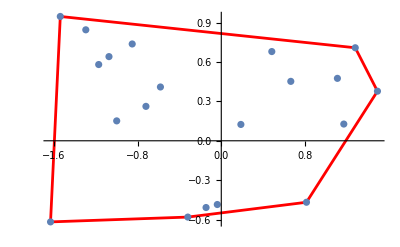

```mathematica
gr
```